```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop-Debug"}]]
(*SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop_Qt_5_10_1_MinGW_32bit-Debug"}]]*)
```

/home/v.korchagova/Документы/BMSTU/build-RKDG2D-Desktop-Debug

```mathematica
mesh=Import["mesh2D","Table"];
```

```mathematica
(*nodes*)
offset=2;
nNodes=mesh[[offset,1]];
nodes=Table[mesh[[i]][[2;;]],{i,offset+1,nNodes+offset}];
(*edges*)
offset=3+nNodes+1+1;
nEdgesBoundary=mesh[[offset,1]];
nEdges=mesh[[offset+1,1]];
edges=Table[mesh[[i]][[2;;]],{i,offset+2,nEdges+offset+1}];
(*edge normals*)
offset = nEdges+offset+5;
edgeNormals=Table[mesh[[i]][[2;;]],{i,offset,nEdges+offset-1}];
(*cells*)
offset = offset +nEdges+2;
nCells=mesh[[offset]][[1]];
cells=Table[mesh[[i]][[3;;]],{i,offset+1,nCells+offset}];
(*cell centers*)
offset = offset +nCells+4;
cellCenters=Table[mesh[[i]][[2;;]],{i,offset,nCells+offset-1}];
(*patches*)
offset=offset+nCells+2;
nPatches=mesh[[offset]][[1]];
offset = offset+1;
patchNames={};
patchEdgeGroups={};
For[i=1,i≤nPatches, ++i,
{
patchNames=Append[patchNames,mesh[[offset,2]]];
(*Print[patchNames];*)
nEdgesInPatch=mesh[[offset+1,1]];
(*Print[nEdgesInPatch];*)
patchEdgeGroups = Append[patchEdgeGroups,Table[mesh[[i,1]],{i,offset+2,offset+1+nEdgesInPatch}]];
offset=offset+2+nEdgesInPatch;
(*Print[offset];*)
}];
patchNames
```

{bottom,top,left,right}

```mathematica
(*drawing functions*)
```

```mathematica
drawNode[iNode_]:=Point[nodes[[iNode]]];
drawEdgeArrow[iEdge_]:=Arrow[{nodes[[edges[[iEdge,1]]]],nodes[[edges[[iEdge,2]]]]}];
drawEdgeLine[iEdge_]:=Arrow[{nodes[[edges[[iEdge,1]]]],nodes[[edges[[iEdge,2]]]]}];
drawEdgeNormal[iEdge_]:=Arrow[{(nodes[[edges[[iEdge,1]]]]+nodes[[edges[[iEdge,2]]]])/2,(nodes[[edges[[iEdge,1]]]]+nodes[[edges[[iEdge,2]]]])/2+edgeNormals[[i]]*0.25*Norm[{nodes[[edges[[iEdge,2]]]]-nodes[[edges[[iEdge,1]]]]},2]}];
drawCell[iCell_]:=
Return[{nodes[[edges[[cells[[iCell,1]],1]]]],
nodes[[edges[[cells[[iCell,1]],2]]]],
nodes[[edges[[cells[[iCell,3]],2]]]],
nodes[[edges[[cells[[iCell,3]],1]]]]}];
drawPatch[color_,iPatch_]:={color,Table[drawEdgeLine[patchEdgeGroups[[i,j]]],{j,1,Length[patchEdgeGroups[[i]]]}]};
```

```mathematica
(*pictures*)
```

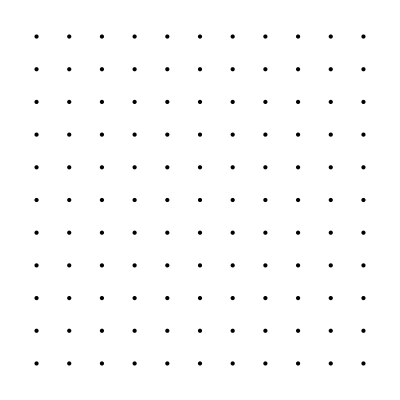

```mathematica
Graphics[Table[drawNode[i],{i,1,nNodes}]]
```

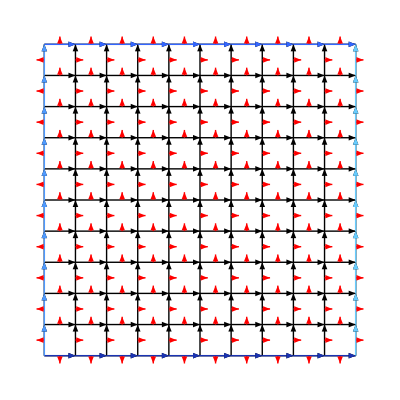

```mathematica
Graphics[{Table[drawEdgeArrow[i],{i,1,nEdges}],
Red,Arrowheads[0.02],
Table[drawEdgeNormal[i],{i,1,nEdges}],Thick,
Table[drawPatch[RGBColor[i*0.1,i*0.2,i*0.7],i],{i,1,nPatches}]}]
```

```mathematica
Manipulate[Graphics[{EdgeForm[Directive[Thick,Black]],Cyan,
Table[Polygon[{drawCell[i]}],{i,1,p}],Black,
Table[Point[{cellCenters[[i]]}],{i,1,p}]},PlotRange->Full],{p,1,nCells}]
```